## General Substitution Scheme

#### Introduction

We assume that the picture will be consist of images under some G of a collection of motifs.

The images will have certain positions, given by matrices; usually we will work with homogeneous coordinates.  Composition/ multiplication is on the left

All we must specify are:

Tiles of type k in position k will be represented by {position, k}

IterateMotif[ {position,k} ]  returns list of  children of a given tile 

xxxMotif[ {position,  k}]     returns  motif as list of (graphics) objects  in position k
ShowxxxMotifs[ {Motif[], Motif[],...} ]   wraps motifs for graphic output

IteratexxxMotif[ {position,k} ]  returns list of  motifs descending from tile
				(Effectively, IteratexxxMotif IS the rule list)

The only commands that are actually run is:

SubInit= {initial Motif, depth, commands,auxiliary} =
					{ {position0,k0}, depth      , 
 							    {xxxMotif, ShowxxxMotifs,IteratexxxMotif},auxiliary}
 
SubIt[SubInit]

ShowIt[SS,SubInit]

#### SubIt

Ive modified this: (11/00)

```mathematica
SubIt[{initlist_,d_,{xM_, SM_,IM_},au_}]:=	


SM[ (xM /@
(au;
	Nest[ Join@@ IM /@ # &, 
 			initlist,d]))]
```

Show all generations:

```mathematica
SubItAll[{{p0_,k0_},d_,{xM_, SM_,IM_},au_}]:=	


SM[ (xM /@
(au;Join @@
	NestList[ Join@@ IM /@ # &, 
 			{{p0,k0}},d]))]
```

#### Numbers

```mathematica
NN[n_]:=Chop[N[n],10^-6]
```

```mathematica
NN[Sqrt[2]-1.414213562]
```

0

### Homogeneous Coordinates:

```mathematica
Unprotect[Translate,Rotate,Scale];
```

Homo2Cart converts a homogeneous (n+1)-tuple to a Cartesian (n)-tuple

```mathematica
Homo2Cart[vect_]:=Drop[vect,-1]/vect[[-1]]

Cart2Homo[vect_]:=Insert[vect,1,Length[vect]+1]
```

These produce the appropriate (dim+1)-dimensional matrices; 
	multiplying on the left of a homogeneous coordinate performs the epynomous act

```mathematica
Ident[dim_]:= Block[{temp=Table[0,{i,1,dim}]},
				Table[Insert[temp,1,i],{i,1,dim+1}]]
```

```mathematica
Scale[s_,dim_]:= s ReplacePart[Ident[dim],1/s,{-1,-1}]
```

```mathematica
Translate[vect_,dim_]:=Transpose[(*switching to right*)
	Block[{iii=1,temp=Ident[dim]}, While[iii<dim+1,
	temp=ReplacePart[temp,vect[[iii]],{iii,-1}];iii++];temp]]
```

```mathematica
Affine[matr_,dim_]:=
	Block[{iii=1,temp=matr}, While[iii<dim+1,
	temp=Insert[temp,0,{iii,dim+1}];iii++];
		Join[temp,{Join[Table[0,{ii,1,dim}],{1}]}]]
```

2d only:

```mathematica
Rotate[angle_]:=
	{{Cos[angle],Sin[angle],0},{-Sin[angle],Cos[angle],0},{0,0,1}}
```

```mathematica
Reflect[{b_,a_}]:= (*reflect preserving the vector {a,b}*){{-a^2+b^2,2 a b,0}/(a^2+b^2),{2 a b,a^2-b^2,0}/(a^2+b^2),{0,0,1}}
```

```mathematica
Project[vect_,dim_]:=
If[Length[vect]==dim+1,
	Append[
	Append[#,0]& /@ Ident[dim-1],vect],
If[Length[vect]==dim,
	Append[
	Append[#,0]& /@ Ident[dim-1],Append[vect,1]],error]]
```

Project[vect,dim] sends the "plane at infinity" to the plane {x,y,...}.vect
The unit hypercube {{0,0,...,0},....{1,1,...,1}}
is sent to , eg:

0               0               0

                                  1
                                -----
0               0               1 + c

                  1
                -----
0               1 + b           0

                    1               1
                ---------       ---------
0               1 + b + c       1 + b + c

  1
-----
1 + a           0               0

    1                               1
---------                       ---------
1 + a + c       0               1 + a + c

    1               1
---------       ---------
1 + a + b       1 + a + b       0

      1               1               1
-------------   -------------   -------------
1 + a + b + c   1 + a + b + c   1 + a + b + c

#### Examples

```mathematica
Ident[3] //MatrixForm
```

1   0   0   0

0   1   0   0

0   0   1   0

0   0   0   1

```mathematica
Scale[12,4]//MatrixForm
```

1           0           0           0           0

0           1           0           0           0

0           0           1           0           0

0           0           0           1           0

0           0           0           0           0.0833333

```mathematica
Homo2Cart[Scale[12,2].{2,3,1}]
```

{24., 36.}

```mathematica
Cart2Homo[{a,b,c}]
```

{a, b, c, 1}

```mathematica
Translate[{a,b,c},3]//MatrixForm
```

1   0   0   a

0   1   0   b

0   0   1   c

0   0   0   1

```mathematica
Homo2Cart[Translate[{a,b,c},3].{2,3,4,1}]
```

{2 + a, 3 + b, 4 + c}

```mathematica
Affine[{ {a,b,e},{c,d,f},{g,h,i}}, 3]//MatrixForm
```

a   b   e   0

c   d   f   0

g   h   i   0

0   0   0   1

```mathematica
Project[{a,v,c,d},3]//MatrixForm
```

1   0   0   0

0   1   0   0

0   0   1   0

a   v   c   d

```mathematica
Homo2Cart /@ 
(Project[{a,b,c},3].#& /@ {{0,0,0,1},{0,0,1,1},
					  {0,1,0,1},{0,1,1,1},
					  {1,0,0,1},{1,0,1,1},
					  {1,1,0,1},{1,1,1,1}} )//TableForm
```

0               0               0

                                  1
                                -----
0               0               1 + c

                  1
                -----
0               1 + b           0

                    1               1
                ---------       ---------
0               1 + b + c       1 + b + c

  1
-----
1 + a           0               0

    1                               1
---------                       ---------
1 + a + c       0               1 + a + c

    1               1
---------       ---------
1 + a + b       1 + a + b       0

      1               1               1
-------------   -------------   -------------
1 + a + b + c   1 + a + b + c   1 + a + b + c

```mathematica
Homo2Cart/@(Project[{a,b,c},3].#&/@(
Cart2Homo /@
Hypercube[3]))//TableForm
```

Insert::ins: Cannot insert at position {1} in 3.

1
Hypercube[{{---------------, 0, 0, 0}, 
            Insert[3, 1, 1]
 
              1                              1
   {0, ---------------, 0, 0}, {0, 0, ---------------, 0}, 
       Insert[3, 1, 1]                Insert[3, 1, 1]
 
           a                b                c
   {---------------, ---------------, ---------------, 
    Insert[3, 1, 1]  Insert[3, 1, 1]  Insert[3, 1, 1]
 
           1
    ---------------}}]
    Insert[3, 1, 1]

### A New Triangle Example

For any j and k, we will construct an example with inflation factor s, where s is the real positive root of s^k+s^(k+2j)=1. I don't know why there is only one such positive root.
The tile X will be a triangle with sides 1,s,s^2.  The triangle will appear in k sizes  s^0, s^1,... s^(k-1) There are two ways of filling this triangle in, with four triangles of sizes s^k,2× s^(k+j), s^(k+2j) as illustrated below.  Consequently we will use two colors, to distinguish which rule to use. There are thus 2^8distinct possible substitution rules for each choice of j and k.

Oddly, note  that when j=1, k=2, Cos[angle opp edge of length s^k+2j] = 1/ϕ

```mathematica
aux=(		
		

		Unprotect[A,B,s,j,k];
		Clear[sc];
		
		j = 1; k=1;
		
		s=(Select[Select[ss/.Solve[ss^k+ss^(k+2j)==1,ss],Head[#//N]==Real&],N[#]>0&]//N)⟦1⟧;
		
		angles = ArcCos[
		(-#⟦1⟧^2+#⟦2⟧^2+#⟦3⟧^2)/(2#⟦2⟧ #⟦3⟧)]&/@
		Table[RotateLeft[{1,s,s^2},k],{k,0,2}];

		apex = s{Cos[angles⟦3⟧],Sin[angles⟦3⟧]};
		hapex=Append[apex,1];
		ident={{1,0,0},{0,1,0},{0,0,1}};

		rx={{-1,0,0},{0,1,0},{0,0,1}};
		sc[n_]:=sc[n]=Scale[s^n,2];
		
	rules[A]={B,A,A,B};
		rules[B]={B,A,B,A};	
		
		moves[A]={
				sc[k],
				Translate[-apex,2].
						sc[k+j].rx.Rotate[angles⟦3⟧-angles⟦2⟧].Translate[apex,2],
			sc[k+j].rx.Rotate[angles⟦3⟧-angles⟦2⟧+π].Translate[s^k  apex,2],
				Translate[{-1,0},2].sc[k+2j].Translate[{1,0},2]
			
			};
		
		moves[B]={
				sc[k+j].rx.Rotate[π+angles⟦3⟧],
				
				Translate[-apex,2].sc[k+2j].Translate[apex,2],
			
					Translate[-apex,2].sc[k+j].rx.Rotate[angles⟦3⟧].Translate[s^k apex,2],
					
				Translate[{-1,0},2].sc[k].Translate[{1,0},2]
			
			};
		
				
		sizes[A]={k,k+j,k+j,k+2j};
		sizes[B]={k+j,k+2j,k+j,k};
		
		pColor[A]=GrayLevel[.7];
		lColor[A]=GrayLevel[0];
		pColor[B]=GrayLevel[.9];
		lColor[B]=GrayLevel[0];
		
		pColor[A,n_]:=pColor[A,n]=GrayLevel[.95 (n/(k+2j))];
		pColor[B,n_]:=pColor[B,n]=RGBColor @@ ({1,.5,1}.7 (n/(k+2j)));
		
Protect[A,B,s,j,k];
		
		)
```

```mathematica
sub[{pos_,X_[n_]}]/;n>0:={{pos,X[n-1]}};
sub[{pos_,X_[0]}]:=
	Table[{moves[X]⟦k⟧.pos,rules[X]⟦k⟧[sizes[X]⟦k⟧]},{k,1,4}]
```

```mathematica
draw[{pos_,X_[n_]}]:=
	{pColor[X,n],Polygon[#],lColor[X],Line[Append[#,#⟦1⟧]&[#]]}&@(Homo2Cart/@(#.pos&/@ {{0,0,1},{1,0,1},hapex}))
```

```mathematica
show[dlist_,opts___]:=Show[Graphics[Join @@ dlist,opts,AspectRatio->Automatic]]
```

```mathematica
Clear[ddepth,sstart];
```

```mathematica
init={
		{{{{1,0,0},{0,1,0},{0,0,1}},sstart[0]}},
	ddepth,{draw,show,sub},i:=.01};
```

```mathematica
ddepth=2;sstart=A;
```

```mathematica
rules[A]={B,A,A,B};
		rules[B]={B,A,B,A};
```

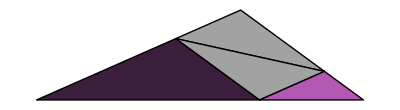

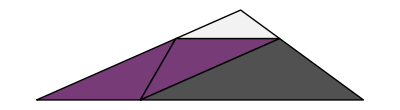

```mathematica
SubIt[	{{{{{1,0,0},{0,1,0},{0,0,1}},A[0]}},
	1,{draw,show,sub},i}]
SubIt[	{{{{{1,0,0},{0,1,0},{0,0,1}},B[0]}},
	1,{draw,show,sub},i}]
```

```mathematica
ddepth=40
```

40

```mathematica
SubIt[ init]
```

⁃Graphics⁃

```mathematica
rules[A]={A,A,A,A};
		rules[B]={B,B,B,B};
```

```mathematica
ddepth=1;sstart=A;
SubIt[init];sstart=B;
SubIt[	init]
```

⁃Graphics⁃

```mathematica
Table[ddepth=i;sstart=A;SubIt[init],{i,1,55}]
```

{⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃,⁃Graphics⁃}

```mathematica
rules[A]={A,B,B,A};
		rules[B]={A,B,A,B};
```

```mathematica
SubIt[	{{{{{1,0,0},{0,1,0},{0,0,1}},A[0]}},
	1,{draw,show,sub},i}]
SubIt[	{{{{{1,0,0},{0,1,0},{0,0,1}},B[0]}},
	1,{draw,show,sub},i}]
```

⁃Graphics⁃

⁃Graphics⁃

```mathematica
ddepth=11
SubIt[ init]
```

11

⁃Graphics⁃

### Another New Triangle Example

For any j and k, we will construct an example with inflation factor s, where s is the real positive root of s^k+s^(k+2j)=1. I don't know why there is only one such positive root.
The tile X will be a triangle with sides 1,s^j,√(s^(2j)+1).  The triangle will appear in k sizes  s^1, s^2,... s^(k+2j) There is one way of filling in s^0, with four triangles of sizes s^k,2× s^(k+j), s^(k+2j)  all of the same orientation, as illustrated below.

```mathematica
aux=(		
		

		Unprotect[A,B,s,j,k];
		Clear[sc];
		
		j = 1; k=1;
		
		s=(Select[Select[ss/.Solve[ss^k+ss^(k+2j)==1,ss],Head[#//N]==Real&],N[#]>0&]//N)⟦1⟧;
		
		angles = ArcCos[
		(-#⟦1⟧^2+#⟦2⟧^2+#⟦3⟧^2)/(2#⟦2⟧ #⟦3⟧)]&/@
		Table[RotateLeft[{1,s,√(1+s^2)},k],{k,0,2}];

		apex = s{Cos[angles⟦3⟧],Sin[angles⟦3⟧]};
		hapex=Append[apex,1];
		ident={{1,0,0},{0,1,0},{0,0,1}};

		rx={{-1,0,0},{0,1,0},{0,0,1}};
		sc[n_]:=sc[n]=Scale[s^n,2];
		
		rules[B]={B,B,B,B};	
		
	moves[B]={
				sc[k+j].Rotate[angles⟦3⟧].Translate[{s^(2j+k),0},2],
				
				Translate[-apex,2].sc[k+2j].Translate[apex,2],
			
				sc[k+j].Rotate[π+angles⟦3⟧].Translate[s^k apex,2],
					
				Translate[{-1,0},2].sc[k].Translate[{1,0},2]
			
			};
		
				
	sizes[B]={k+j,k+2j,k+j,k};
		
	pColor[B]=GrayLevel[.9];
		lColor[B]=GrayLevel[0];
		
Protect[A,B,s,j,k];
		
		)
```

```mathematica
sub[{pos_,X_[n_]}]/;n>0:={{pos,X[n-1]}};
sub[{pos_,X_[0]}]:=
	Table[{moves[X]⟦k⟧.pos,rules[X]⟦k⟧[sizes[X]⟦k⟧]},{k,1,4}]
```

```mathematica
draw[{pos_,X_[n_]}]:=
	{pColor[X],Polygon[#],lColor[X],Line[Append[#,#⟦1⟧]&[#]]}&
			
[Homo2Cart/@(#.pos&/@ {{0,0,1},{1,0,1},hapex})]
```

```mathematica
show[dlist_,opts___]:=Show[Graphics[Join @@ dlist,opts,AspectRatio->Automatic]]
```

```mathematica
Clear[ddepth,sstart];
```

```mathematica
init={
		{{{{1,0,0},{0,1,0},{0,0,1}},sstart[0]}},
	ddepth,{draw,show,sub},i:=.01};
```

```mathematica
ddepth=2;sstart=B;
```

```mathematica
SubIt[	{{{{{1,0,0},{0,1,0},{0,0,1}},B[0]}},
	1,{draw,show,sub},i}]
```

⁃Graphics⁃

```mathematica
ddepth=40
```

40

```mathematica
SubIt[ init]
```

⁃Graphics⁃